Universidad de Jaén. EPS Jaén.
Departamento de Matemáticas. Grado en Ingeniería Informática
Análisis y Métodos Numéricos.

## Problemas. Tema 9. Ecuaciones diferenciales

## 1.- Problema del enfriamiento del café. Suponemos la ley de enfriamiento de Newton, y’=K(M-y), donde M es la temperatura del medio ambiente, K una constante que depende de cómo se pierde el calor e y(x) la temperatura del café en el momento x. Supongamos que M=20 grados, y(0)=80 e y(1)=70, encontrar y(x). ¿Cuándo y(x)=35 o y(x)=25?

Solución: 
Tenemos el problema de valores iniciales
									{y'=k(20-y)
y(0)=80
más una condición extra y(1)=70.

Comenzamos resolviendo la ecuación diferencial y’=K(20-y), la cual se trata de una ecuación diferencial lineal de variables separadas

y’=k(20-y)
dy/(20-y)=k
∫ⅆy/(20-y)=∫kⅆt
-Ln(20-y)=kt+C_1
20-y=e^(-kt+C_1)
y(t)=20-e^(-kt+C_1)
y(t)=20-e^C_1 e^-kt
y(t)=20-Ce^-kt

Para obtener los valores de C basta con imponer la condición inicial
y(0)=80 ⟹20-Ce^(-k*0)=80⟹20-C=80⟹C=-60

Como tenemos una condición extra podemos también calcular el valor de k
y(1)=70 ⟹20+60 e^(-k*1)=70⟹60 e^-k=50⟹e^-k=5/6⟹-k=Ln(5/6)⟹k=-Ln(5/6)⟹k≃0.182322

La solución del problema de enfriamiento del café viene dada por

y(t)=20+60 e^(Ln(5/6)t)=20+60(e^(Ln(5/6)))^t=20+60(5/6)^t

Para saber cuando y(t)=35 basta con resolver la ecuación

y(t)=35⟹20+60(5/6)^t=35⟹60(5/6)^t=15⟹(5/6)^t=1/4⟹t*Ln(5/6)=Ln(1/4)⟹t=(Ln(1/4))/(Ln(5/6))⟹t≃7.60357

La temperatura bajará hasta los 35 grados en 7.6 minutos.

Igual procedemos para saber cuando y(t)=25

y(t)=25⟹20+60(5/6)^t=25⟹60(5/6)^t=5⟹(5/6)^t=1/12⟹t*Ln(5/6)=Ln(1/12)⟹t=(Ln(1/12))/(Ln(5/6))⟹t≃13.6293

La temperatura bajará hasta los 25 grados en 13.6 minutos.

Con Mathematica

Podemos pedirle únicamente que resuelva la ecuación diferencial

```mathematica
DSolve[y'[x]==k (20-y[x]),y[x],x]
```

{{y[x]→20+ⅇ^(-k x) C[1]}}

Otra posibilidad, más rápida, es pedir que resuelva la ecuación y la condición inicial:

```mathematica
DSolve[{y'[x]==k (20-y[x]),y[0]==80},y[x],x]
```

{{y[x]→20 ⅇ^(-k x) (3+ⅇ^(k x))}}

```mathematica
y[x_]:= 20 ⅇ^(-k x) (3+ⅇ^(k x))
```

Aquí no conocemos el valor de k, pues dependerá de diversas cuestiones como el aislamiento del recipiente, de la velocidad del aire, etc. Para salvar este problema, usamos una segunda medición de la temperatura al minuto.

```mathematica
Solve[y[1]==70,k,Reals]
```

{{k→Log[2]+Log[3]-Log[5]}}

```mathematica
k=Log[2]+Log[3]-Log[5];
```

Al imponer que la temperatura al minuto sea de 70 grados, obtenemos el valor de k.

```mathematica
y[x]
```

20 ⅇ^(x (-Log[2]-Log[3]+Log[5])) (3+ⅇ^(x (Log[2]+Log[3]-Log[5])))

```mathematica
Solve[y[x]==35,x,Reals]//N
```

{{x→7.60357}}

La temperatura bajará hasta los 35 grados en 7.6 minutos.

```mathematica
Solve[y[x]==25,x,Reals]//N
```

{{x→13.6293}}

La temperatura bajará hasta los 25 grados en 13.6 minutos.

## 2.- La sala de disección de un forense se mantiene fría a una temperatura constante de 5°C. Mientras se encontraba realizando la autopsia de una víctima de asesinato, el propio forense es asesinado. A las 10 am el ayudante del forense descubre su cadáver a una temperatura de 23°C. A las 12 am su temperatura es de 17°C. Suponiendo que el forense tenía en vida la temperatura normal de 37°C, veamos a qué hora fue asesinado

Solución: 
Se trata de un problema de Ley de enfriamiento de Newton, donde la temperatura ambiente es de 5.baC, esto es, M=5.baC. Tomando como tiempo 0 el momento en el que se encuentran el cadáver, 10.00h, se tiene y(0)=23.baC. Por lo que tenemos el problema de valores iniciales
									{y'=k(5-y)
y(0)=23
Además, sabemos que pasadas dos horas, la temperatura del cadáver había descendido hasta los 17.baC, es decir, se tiene que y(2)=17.

Comenzamos resolviendo la ecuación diferencial y’=K(5-y), la cual se trata de una ecuación diferencial lineal de variables separadas

y’=k(5-y)
dy/(5-y)=k
∫ⅆy/(5-y)=∫kⅆt
-Ln(5-y)=kt+C_1
5-y=e^(-kt+C_1)
y(t)=5-e^(-kt+C_1)
y(t)=5-e^C_1 e^-kt
y(t)=5-Ce^-kt

Para obtener los valores de C basta con imponer la condición inicial
y(0)=23 ⟹5-Ce^(-k*0)=23⟹5-C=23⟹C=-18.baC

Como tenemos una condición extra podemos también calcular el valor de k
y(2)=17⟹5+18 e^(-k*2)=17⟹18 e^(-2k)=12⟹e^(-2k)=2/3⟹-2k=Ln(2/3)⟹k=-1/2Ln(2/3)⟹k=-Ln(√(2/3))⟹k≃0.202733

La solución del problema de valores iniciales viene dada por

y(t)=5+18 e^(Ln(√(2/3))t)=5+18(e^(Ln(√(2/3))))^t=5+18(√(2/3))^t

Para saber cuando fue asesinado el forense hay que calcular cuando su cuerpo tenía una temperatura de 37.baC, que es la temperatura que tomamos como referencia de un cuerpo humano normal. Es decir, debemos calcular para que tiempo t se tiene que y(t)=37

y(t)=37⟹5+18(√(2/3))^t=37
⟹18(√(2/3))^t=32⟹(√(2/3))^t=16/9⟹t*Ln(√(2/3))=Ln(16/9)⟹t=(Ln(16/9))/(Ln(√(2/3)))⟹t≃-2.83805h⟹t≃-2h 50min

Es decir, el forense fue asesinado 2h y 50min antes de que lo encontrara su ayudante a las 10.00 am. Por lo que podemos estimar la hora de la muerte a las 7h 10min de la mañana

Con Mathematica

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[{y'[t]==k (5-y[t]),y[0]==23},y[t],t]//Simplify
```

{{y[t]→5+18 ⅇ^(-k t)}}

```mathematica
y[t_]:= 5+18 ⅇ^(-k t)
```

Para determinar el valor de k, imponemos la temperatura del cuerpo pasadas las 2h

```mathematica
Solve[y[2]==17,k,Reals]
```

{{k→1/2 (-Log[2]+Log[3])}}

```mathematica
k=1/2 (-Log[2]+Log[3]);
```

```mathematica
y[t]
```

5+18 ⅇ^(1/2 t (Log[2]-Log[3]))

Para hallar la hora de la muerte buscamos el punto t donde la temperatura del cuerpo era de 37.baC

```mathematica
Solve[y[t]==37,t,Reals]//N
```

{{t→-2.83805}}

El cuerpo se encontraba vivo 2.83805h antes del tiempo tomado como inicial (t=0 a las 10.00h). Esto es, 2h 50min antes de las 10.00h, es decir, el forense fue asesinado a las 7h 10min de la mañana

## 3.- Un ganadero salió una tarde a cazar un lobo solitario que estaba diezmando su rebaño. El cuerpo del ganadero fue encontrado sin vida por un campesino, en un cerro cerca del rancho junto al animal cazado, a las 6:00 h del día siguiente. Un médico forense llegó a las 7:00 y tomó la temperatura del cadáver, a esa hora anotó 23℃; una hora más tarde, al darse cuenta de que en la noche, y aún a esas horas, la temperatura ambiente era aproximadamente de 5℃, el médico volvió a medir la temperatura corporal del cadáver y observó que era de 18,5℃. ¿A qué hora murió el ganadero aproximadamente?

Solución: 
Se trata de un problema de Ley de enfriamiento de Newton, donde la temperatura ambiente es de 5.baC, esto es, M=5.baC. Tomando como tiempo 0 el momento en el que el forense toma la primera medición de temperatura del cadáver, 7.00h, se tiene y(0)=23.baC. Por lo que tenemos el problema de valores iniciales
									{y'=k(5-y)
y(0)=23
									
Además, sabemos que pasada una hora, la temperatura del cadáver había descendido hasta los 18.5.baC, es decir, se tiene que y(1)=18.5.

Comenzamos resolviendo la ecuación diferencial y’=K(5-y), la cual se trata de una ecuación diferencial lineal de variables separadas

y’=k(5-y)
dy/(5-y)=k
∫ⅆy/(5-y)=∫kⅆt
-Ln(5-y)=kt+C_1
5-y=e^(-kt+C_1)
y(t)=5-e^(-kt+C_1)
y(t)=5-e^C_1 e^-kt
y(t)=5-Ce^-kt

Para obtener los valores de C basta con imponer la condición inicial
y(0)=23 ⟹5-Ce^(-k*0)=23⟹5-C=23⟹C=-18.baC

Como tenemos una condición extra podemos también calcular el valor de k
y(1)=18.5⟹5+18 e^(-k*1)=18.5⟹18 e^-k=13.5⟹e^-k=13.5/18=0.75⟹-k=Ln(0.75)⟹k=-Ln(0.75)⟹k=-Ln(0.75)⟹k≃0.287682

La solución del problema de valores iniciales viene dada por

y(t)=5+18 e^(Ln(0.75)t)=5+18(e^(Ln(0.75)))^t=5+18(0.75)^t

Para saber cuando fue asesinado el cazador hay que calcular cuando su cuerpo tenía una temperatura de 37.baC, que es la temperatura que tomamos como referencia de un cuerpo humano normal. Es decir, debemos calcular para que tiempo t se tiene que y(t)=37

y(t)=37⟹5+18(0.75)^t=37
⟹18(0.75)^t=32⟹(0.75)^t=16/9⟹t*Ln(0.75)=Ln(16/9)⟹t=(Ln(16/9))/(Ln(0.75))⟹t≃-2h

Es decir, el cazador fue asesinado 2h antes de que llegara el forense a las 7.00 am. Por lo que podemos estimar la hora de la muerte a las 5h de la mañana

Con Mathematica

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[{y'[t]==k (5-y[t]),y[0]==23},y[t],t]//Simplify
```

{{y[t]→5+18 ⅇ^(-k t)}}

```mathematica
y[t_]:= 5+18 ⅇ^(-k t)
```

Para determinar el valor de k, imponemos la temperatura del cuerpo pasadas las 2h

```mathematica
Solve[y[1]==18.5,k,Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{k→0.287682}}

```mathematica
k=0.2876820724517809;
```

```mathematica
y[t]
```

5+18 ⅇ^(-0.287682 t)

Para hallar la hora de la muerte buscamos el punto t donde la temperatura del cuerpo era de 37.baC

```mathematica
Solve[y[t]==37,t,Reals]//N
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{t→-2.}}

El cuerpo se encontraba vivo 2h antes del tiempo tomado como inicial (t=0 a las 7.00h). Esto es, el cazador fue asesinado a las 5h de la mañana

## 4.- Una sustancia es retirada de un horno y llevada a un área de enfriamiento que mantiene una temperatura estable de 43°C, a los 15 y 30 minutos después de haberse iniciado el enfriamiento se realizaron dos registros de temperatura, que arrojaron como resultado 285°C y 252 °C, respectivamente. Determinar: a) La temperatura inicial de la sustancia. b) En que instante la temperatura del cuerpo es de 80 °C.

Solución: 
Se trata de un problema de Ley de enfriamiento de Newton, donde la temperatura ambiente es de 43.baC, esto es, M=43.baC, con el tiempo t medido en minutos. Se tiene así la ecuación diferencial y’=k(43-y)
En este caso, no nos dan condición inicial pero si nos dan las mediciones a las 15 y a los 30 min, es decir, tenemos y(15)=285.baC e y(30)=252.baC

Resolvemos la ecuación diferencial la cual se trata de una ecuación diferencial lineal de variables separadas

y’=k(43-y)
dy/(43-y)=k
∫ⅆy/(43-y)=∫kⅆt
-Ln(43-y)=kt+C_1
43-y=e^(-kt+C_1)
y(t)=43-e^(-kt+C_1)
y(t)=43-e^C_1 e^-kt
y(t)=43-Ce^-kt

Imponemos ahora las dos mediciones de temperatura realizadas obteniendo así un sistema de ecuaciones 
y(15)=285⟹43-Ce^(-k*15)=285⟹-Ce^(-15k)=242⟹C=242 e^(15k)
y(30)=252⟹43-Ce^(-k*30)=252⟹-Ce^(-30k)=209⟹-242 e^(15k)*e^(-30k)=209⟹e^(-15k)=-19/22⟹-15k=Ln(-19/22)⟹k=-1/15Ln(-19/22)
⟹C=242e^(-Ln(-19/22))⟹C=242*22/19⟹C=5324/19

La solución de la ecuación diferencial viene dada por

y(t)=43+5324/19(-19/22)^(t/15)

Para hallar la condición inicial basta calcular y(0)

y(0)=43+5324/19 e^(1/15 Ln(-19/22)*0)=43+5324/19=(817+5324)/19=6141/19

Para hallar el punto t en el cual la sustancia tenía una temperatura de 80, debemos de resolver la ecuación y(t)=80

y(t)=80⟹43+5324/19(-19/22)^(t/15)=80⟹5324/19(-19/22)^(t/15)=37⟹(-19/22)^(t/15)=703/5324⟹t/15Ln(-19/22)=Ln(703/5324)⟹t=(Ln(703/5324))/(1/15 Ln(-19/22))≃73.2138

La sustancia tendrá una temperatura de 80.baC pasados 73.2138min, es decir, 1h 13min desde que es retirada del horno

Con Mathematica

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[y'[t]==k (43-y[t]),y[t],t]//Simplify
```

{{y[t]→43+ⅇ^(-k t) C[1]}}

```mathematica
y[t_]:= 43+ⅇ^(-k t) *c
```

Para determinar el valor de las constantes C y k, imponemos los valores de las dos mediciones de temperatura realizadas

```mathematica
Solve[{y[15]==285,y[30]==252},{k,c},Reals]
```

{{k→1/15 (Log[2]+Log[11]-Log[19]),c→5324/19}}

```mathematica
k=1/15 (Log[2]+Log[11]-Log[19]);
c=5324/19;
```

```mathematica
y[t]
```

43+5324/19 ⅇ^(1/15 t (-Log[2]-Log[11]+Log[19]))

Para hallar la condición inicial, vemos cuanto vale la función y(t) en 0, esto es, y(0)

```mathematica
y[0]
```

6141/19

```mathematica
Solve[y[t]==180,t, Reals]//N
```

{{t→73.2138}}

La sustancia tendrá una temperatura de 80.baC pasados 73.2138min, es decir, 1h 13min desde que es retirada del horno

## 5.- Depreciación de un vehículo Supongamos que el precio de un vehículo, P(t), se deprecia un 10% anual y que cada año se le realizan tareas de mantenimiento por un importe de 300 euros. Si inicialmente el valor era de 30.000 euros, calcular, resolviendo la ecuación diferencial P’(t) = -0.1P(t)+300, la función P(t).

Solución: 
Se trata de resolver el problema de valores iniciales
{P'=-0.1P(t)+300
P(0)=30000
Comenzaremos resolviendo la ecuación diferencial, P’+0.1P = 300. Se trata de una ecuación diferencial de primer orden lineal con coeficientes constantes completa. Para resolverla, comenzamos con la homogénea:  P’+0.1P = 0.
Asociamos la ecuación algebraica (o polinómica): x+0.1=0. Su solución es x=-0.1.
La solución general de la ecuación diferencia homogénea es C e^(-0.1 t), con C número real cualquiera.

Para hallar una solución particular de la completa, y a la vista de que el término independiente es una constante, probaremos con constantes:
y(t)=k
Derivamos:	y’(t)=0
Sustituimos en la ecuación diferencial completa: 0+0.1 k=300. De donde obtenemos que k=3000. Por tanto, la solución particular de la completa es 3000.

La solución general de la completa sería la suma de ambas: P(t) = 3000 + C e^(-0.1 t), con C número real cualquiera.

Para resolver el problema de valores iniciales, imponemos la condición inicial y calculamos el valor de la constante C.
P(0) = 3000 + C e^(-0.1 *0) = 3000 + C = 30000, de donde C=27000.

La solución del problema de valores iniciales es P(t) = 3000 + 27000 e^(-0.1 t).

Con Mathematica

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[{P'[t]==-0.1P[t]+300,P[0]==30000},P[t],t]//Simplify
```

{{P[t]→3000.+27000. ⅇ^(-0.1 t)}}

## 6.- La resonancia Al estudiar la ecuaciones diferenciales lineales de grado superior con coeficientes constantes, consideramos primero la parte homogénea y luego buscamos una solución particular de la completa. Para buscar una solución de la completa, consideramos funciones similares a las que hay en el término independiente. Consideremos la ecuación y’’+y=0 con condiciones y(0)=0, y’(0)=1.

Solución:

```mathematica
DSolve[y''[x]+y[x]==0,y[x],x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

```mathematica
DSolve[{y''[x]+y[x]==0,y[0]==0,y'[0]==1},y[x],x]
```

{{y[x]→Sin[x]}}

La solución es la función seno (en realidad, las soluciones de la ecuación diferencial deben ser combinaciones lineales de las funciones seno y coseno. Al imponer las condiciones iniciales, aparece en este caso la función seno)

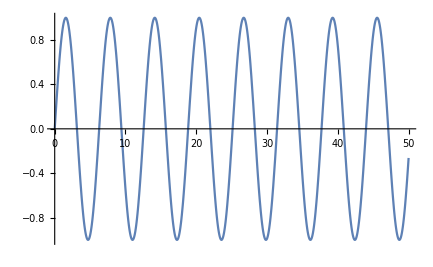

```mathematica
Plot[Sin[x],{x,0,50}]
```

Si introducimos una función en el término independiente, la solución se modifica.

```mathematica
DSolve[{y''[x]+y[x]==1,y[0]==0,y'[0]==1},y[x],x]
```

{{y[x]→1-Cos[x]+Sin[x]}}

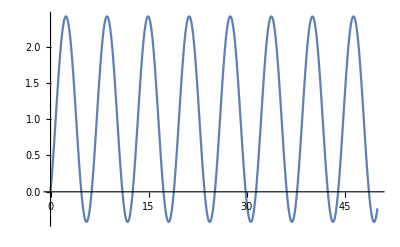

```mathematica
Plot[1-Cos[x]+Sin[x],{x,0,50}]
```

Por ejemplo, al poner la función constante 1, la solución es 1-cos x + sen x. Se trata de una función “similar” a la inicial.

```mathematica
DSolve[y''[x]+y[x]== Cos[a x],y[x],x]//Simplify
```

{{y[x]→1/(-1+a^2)((-1+a^2) C[1] Cos[x]-Cos[a x]+(-1+a^2) C[2] Sin[x])}}

Si ponemos como término independiente cos(ax) la solución es similar, salvo que a sea 1 o -1. Recordemos que si el término independiente es cos(ax) probaríamos con funciones del tipo A cos(ax) + B sen(ax), salvo que a sea 1 o -1, pues debemos probar con funciones del tipo  Ax cos(ax) + Bx sen(ax). En este caso, las soluciones no serían acotadas.

```mathematica
DSolve[{y''[x]+y[x]==Cos[a x]/20,y[0]==0,y'[0]==1},y[x],x]
```

{{y[x]→1/(2 (-1+a^2))(Cos[x]-Cos[x]^2 Cos[a x]-2 Sin[x]+2 a^2 Sin[x]-Cos[a x] Sin[x]^2)}}

Cuando a = 1 es cuando deja de estar acotada porque es cuando el término independiente se parece a la solución. Es una solución de la homogénea. Sería la mejor forma de “empujar al columpio” o al muelle para que oscile más. No es importante que el término independiente sea muy grande o no ( de hecho al dividirlo por 20, sigue ocurriendo lo mismo. Si a es distinto de 1 o -1, no hay mucha diferencia. Si a es 1 o -1, aparece una solución no acotada.)

Este fenómeno se llama de resonancia. Con una fuerza “pequeña”, pero con una frecuencia adecuada se consiguen cosas “sorprendentes”; copas de cristal que se rompen con la voz, puentes que se caen por el viento o al desfilar los soldados, columpios, los receptores de radio, etc. En todos ellos, lo importante es que la fuerza se produzca con la frecuencia adecuada.

```mathematica
Manipulate[Plot[1/(2 (-1+a^2))(Cos[x]-Cos[x]^2 Cos[a x]-2 Sin[x]+2 a^2 Sin[x]-Cos[a x] Sin[x]^2),{x,0,50}],{a,0,2}]
```

Mientras el parámetro a está lejos del 1, la solución es “similar”; funciones acotadas. Cuando a se acerca al 1, la función empieza a tomar valores mayores y aparecen funciones no acotadas.

## 7.- (Enero 2018) Resolver la ecuación diferencial y’’ - 4y = 4 t^2 + 2.

Solución:
Se trata de una ecuación diferencial lineal con coeficientes constantes de segundo orden completa. Para encontrar sus soluciones comenzamos estudiando la ecuación diferencial homogénea asociada; y’’ - 4y = 0. Para resolverla consideramos la ecuación polinómica asociada X^2-4=0.  Las soluciones de esta ecuación son 2 y -2. Por tanto, la solución general de la ecuación diferencial homogénea es y_h(t) = C_1 ⅇ^(2t) + C_2 ⅇ^(-2t), donde C_1 y C_2 son dos constantes reales cualesquiera.

Una vez resuelta la homogénea, pasamos a estudiar la ecuación completa y buscar una solución particular. Dado que el término independiente es un polinomio de segundo grado, intentamos encontrar una solución que sea un polinomio de segundo grado:
	y_p(t) = A t^2+ B t + C
Derivamos
	y_p'(t) = 2A t + B
	y_p’’(t) = 2A
Sustituimos
	y_p’’ - 4y_p = 2A - 4(A t^2+ B t + C) = - 4A t^2- 4 B t + 2A-4C = 4 t^2 + 2.
Igualando los coeficientes de las potencias de t, obtenemos -4A=4, -4B=0, 2A-4C=2. Por tanto, A=-1, B=0, C=-1.
La solución particular es y_p(t) = - t^2-1.
La solución general de la ecuación diferencial completa es la suma de la solución general de la homogénea y la particular de la completa.
	y(t)= - t^2-1 + C_1 ⅇ^(2t) + C_2 ⅇ^(-2t), donde C_1 y C_2 son dos constantes reales cualesquiera

Con Mathematica

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[y''[t]-4y[t]==4t^2+2,y[t],t]
```

{{y[t]→-1-t^2+ⅇ^(2 t) C[1]+ⅇ^(-2 t) C[2]}}

## 8.- (Enero 2018. Aula de Informática) Una sustancia radiactiva se está desintegrando según la ecuación diferencial y’= - K y, para una cierta constante K sabiendo que y(0)=40 e y(2)=20, calcular y(5).

Solución: 
La solución de la ecuación diferencial y’=-K y es y(x)= C ⅇ^-Kx con C número real. Imponiendo que y(0) sea 40, tenemos que C=40. 
Como y(2) debe ser 20 tenemos que y(2)= 40 ⅇ^(-2K) = 20. Despejamos: ⅇ^(-2K)=1/2. Tomamos logaritmos, -2K = log(1/2). K= (-ln(1/2))/2. 
Por tanto, y(x)= 40 ⅇ^-Kx = 40 (1/2)^(x/2). 
Evaluando en x=5, y(5)=40 (1/2)^(5/2)=5√2

Con Mathematica

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[{y'[t]==-k*y[t],y[0]==40},y[t],t]
```

{{y[t]→40 ⅇ^(-k t)}}

```mathematica
y[t_]:=40 ⅇ^(-k t)
```

```mathematica
Solve[y[2]==20,k,Reals]
```

{{k→Log[2]/2}}

```mathematica
k=Log[2]/2;
```

```mathematica
y[t]
```

5 2^(3-t/2)

```mathematica
y[5]
```

5 √2

## 9.- (Julio 2018) Resolver la ecuación diferencial y’ - y = x + e^x.

Solución:
Se trata de una ecuación diferencial lineal con coeficientes constantes de primer orden completa. Para encontrar sus soluciones comenzamos estudiando la ecuación diferencial homogénea asociada; y’ - y = 0. Para resolverla consideramos la ecuación polinómica asociada X-1=0.  La solución de esta ecuación 1. Por tanto, la solución general de la ecuación diferencial homogénea es y_h(x) = C_1 ⅇ^x  donde C_1 es una constante real cualesquiera.

Una vez resuelta la homogénea, pasamos a estudiar la ecuación completa y buscar una solución particular. Dado que el término independiente es una suma de polinomio de primer grado y exponencial, intentamos encontrar una solución que sea suma de polinomio de primer grado y exponencial. Vemos también que ⅇ^x es solución de la homogénea. Por ello, probamos con funciones del tipo:
	y_p(x) = A x ⅇ^x+ B x + C
Derivamos
	y_p'(x) = A ⅇ^x + A x ⅇ^x+ B
Sustituimos
	y_p’ - y_p = A ⅇ^x + A x ⅇ^x+ B -  (A x ⅇ^x+ B x + C) = A ⅇ^x +  B -  B x - C 

que debe ser igual a  x +  ⅇ^x 
Igualando,  
A ⅇ^x +  B -  B x - C  = x +  ⅇ^x 

A debe ser 1, B debe ser -1 y C debe ser igual a B. 

Por tanto, A=1, B=-1, C=-1.

La solución particular es y_p(x) = x ⅇ^x - x -1
La solución general de la ecuación diferencial completa es la suma de la solución general de la homogénea y la particular de la completa.
	y(x) = x ⅇ^x - x -1 + C_1 ⅇ^x , donde C_1 es una constante real cualquiera.
Con el Mathematica podemos comprobar también la solución.

Con Mathematica

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[y'[x]-y[x]==x+Exp[x],y[x],x]//Simplify
```

{{y[x]→-1+(-1+ⅇ^x) x+ⅇ^x C[1]}}

## 10.- (Julio 2018. Aula de Informática) Dado el problema de valores iniciales y’ = 2 y (20-y) con y(3)=5, escribir y(4) con 8 cifras decimales.

Solución:
Se trata de resolver el problema de valores iniciales
{y'=2y(20-y)
y(3)=5
donde la ecuación diferencial y’=2y(20-y) es una ecuación de variables separadas

y’=2y(20-y)
dy/(2y(20-y))=1
∫ⅆy/(2y(20-y))=∫1ⅆt
(Ln(y) -Ln(20-y))/40=t+C_1
Ln(y/(20-y))=40(t+C_1)
y/(20-y)=e^(40t+C_2)
y=(20-y)e^(40t+C_2)
y=20 e^(40t+C_2)-ye^(40t+C_2)
y+ye^(40t+C_2)=20 e^(40t+C_2)
y(1+e^(40t+C_2))=20 e^(40t+C_2)
y=(20 e^(40t+C_2))/(1+e^(40t+C_2))
y(x)=(20 Ce^(40t))/(1+Ce^(40t))

Dividimos por la constante C para arreglar y que nos aparezca una única vez la constante

y(x)=(20 e^(40t))/(1/C+e^(40t))
y(x)=(20 e^(40t))/(K+e^(40t))

imponemos ahora la condición inicial para sacar el valor de la constante K
y(3)=5⟹(20 e^120)/(K+e^120)=5⟹20 e^120=5(K+e^120)⟹20 e^120=5K+5e^120⟹20 e^120-5 e^120=5K⟹15 e^120=5⟹K=(15 e^120)/5⟹K=3 e^120

Así

y(x)=(20 e^(40t))/(3 e^120+e^(40t))

y por tanto

y(4)=(20 e^160)/(3 e^120+e^160)=(e^120(20 e^40))/(e^120(3+e^40))=(20 e^40)/(3+e^40)

Con Mathematica

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[y'[x]==2y[x](20-y[x]),y[x],x]
```

{{y[x]→(20 ⅇ^(40 x))/(ⅇ^(40 x)+ⅇ^(20 C[1]))}}

```mathematica
DSolve[{y'[x]==2y[x](20-y[x]),y[3]==5},y[x],x]
```

{{y[x]→(20 ⅇ^(40 x))/(3 ⅇ^120+ⅇ^(40 x))}}

```mathematica
(20 ⅇ^(40 x))/(3 ⅇ^120+ⅇ^(40 x))/.{x->4}//Simplify
```

(20 ⅇ^40)/(3+ⅇ^40)

## 11.- (Enero 2019) Calcular el valor de a para que la función y(x)=1/(1+ax) sea solución de la ecuación diferencial y’ = y^2.

Solución:
Para que la función y(x) sea solución necesitamos que cumpla la ecuación diferencial. Por tanto,
		y’(x) = -a/(1+a x)^2 = (y(x))^2= 1/(1+a x)^2
De donde obtenemos a=-1.

Con Mathematica

```mathematica
Clear["Global`*"]
```

```mathematica
y[x_]:=1/(1+a*x)
```

```mathematica
Solve[y'[x]==(y[x])^2,a,Reals]
```

{{a→-1}}

## 12.- (Enero 2019) Dado el problema de valores iniciales y’ = 2 y (20-y) con y(0)=1, escribir y(0.1) con 8 cifras decimales.

Solución:
Se trata de resolver el problema de valores iniciales
{y'=2y(20-y)
y(0)=1
donde la ecuación diferencial y’=2y(20-y) es una ecuación de variables separadas

y’=2y(20-y)
dy/(2y(20-y))=1
∫ⅆy/(2y(20-y))=∫1ⅆt
(Ln(y) -Ln(20-y))/40=t+C_1
Ln(y/(20-y))=40(t+C_1)
y/(20-y)=e^(40t+C_2)
y=(20-y)e^(40t+C_2)
y=20 e^(40t+C_2)-ye^(40t+C_2)
y+ye^(40t+C_2)=20 e^(40t+C_2)
y(1+e^(40t+C_2))=20 e^(40t+C_2)
y=(20 e^(40t+C_2))/(1+e^(40t+C_2))
y(x)=(20 Ce^(40t))/(1+Ce^(40t))

Dividimos por la constante C para arreglar y que nos aparezca una única vez la constante

y(x)=(20 e^(40t))/(1/C+e^(40t))
y(x)=(20 e^(40t))/(K+e^(40t))

imponemos ahora la condición inicial para sacar el valor de la constante K
y(0)=1⟹20/(K+1)=1⟹20=K+1⟹K=19

Así

y(x)=(20 e^(40t))/(19+e^(40t))

y por tanto

y(0.1)=(20 e^4)/(19+e^4)

Con Mathematica

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[{y'[x]==2 y[x](20-y[x]),y[0]==1},y[x],x]
```

{{y[x]→(20 ⅇ^(40 x))/(19+ⅇ^(40 x))}}

```mathematica
N[(20 ⅇ^4)/(19+ⅇ^4),10]
```

14.83682674

## 13.- (Enero 2020. Aula de Informática) La temperatura de un cuerpo que se está enfriando se aproxima por la solución de la ecuación diferencial y’= K (20-y), para una cierta constante K, sabiendo que y(0)=40 e y(2)=30, calcular y(5).

Solución: 
Tenemos el problema de valores iniciales
									{y'=k(20-y)
y(0)=40
más una condición extra y(2)=30.

Comenzamos resolviendo la ecuación diferencial y’=K(20-y), la cual se trata de una ecuación diferencial lineal de variables separadas

y’=k(20-y)
dy/(20-y)=k
∫ⅆy/(20-y)=∫kⅆt
-Ln(20-y)=kt+C_1
20-y=e^(-kt+C_1)
y(t)=20-e^(-kt+C_1)
y(t)=20-e^C_1 e^-kt
y(t)=20-Ce^-kt

Para obtener los valores de C basta con imponer la condición inicial
y(0)=40 ⟹20-Ce^(-k*0)=40⟹20-C=40⟹C=-20
Así, la solución es de la forma
y(t)=20+20 e^-kt=20(1+e^-kt)

Como tenemos una condición extra podemos también calcular el valor de k
y(2)=30 ⟹20(1+e^(-2k))=30⟹1+e^(-2k)=3/2⟹e^(-2k)=1/2⟹-2k=Ln(1/2)⟹k=(-Ln(2))/2

La solución del problema viene dada por

y(t)=20(1+e^((Ln(2))/2 t))=20(1+(e^(Ln(2)))^(t/2))=20(1+2^(t/2))

Calculemos el valor de y(5)
y(5)=20(1+2^(5/2))=20(1+4 √2)

Con Mathematica

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[{y'[x]==k (20-y[x]),y[0]==40},y[x],x]//Simplify
```

{{y[x]→20 (1+ⅇ^(-k x))}}

```mathematica
y[x_]:=20 (1+ⅇ^(-k x))
```

```mathematica
Solve[y[2]==30,k,Reals]
```

{{k→Log[2]/2}}

```mathematica
k=Log[2]/2;
```

```mathematica
y[x]
```

20 (1+2^(-x/2))

```mathematica
y[5]//N
```

23.5355

## 14.- (Enero 2020) Resolver la ecuación diferencial y’’ + 2y’ - 3y = 10 e^(2 t).

Solución: 
Comenzamos con la ecuación homogénea: y’’ + 2y’ - 3y =0. 
Buscamos las raíces del polinomio asociado: x^2+2x-3=0=(x+3)(x-1), x=1, -3. 
La solución general de la homogénea es y_h(t)=C_1 e^t+C_2 e^(-3 t).
Ahora buscamos una solución particular de la completa del mismo tipo que el término independiente, es decir una exponencial de 2t;
y_p(t)=C e^(2t).
De donde y'_p(t)= 2C e^(2t), y''_p(t)=4C e^(2t)
Sustituimos en la ecuación diferencial: 
4C e^(2t) + 4C e^(2t)- 3C e^(2t) = 10 e^(2 t), de donde 5C e^(2t) = 10 e^(2t) , por tanto C=2.

La solución general de la completa es y_c(t) = 2 e^(2 t)+C_1 e^t+C_2e^(-3 t).

Con Mathematica

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[y''[t]+2y'[t]-3y[t]==10Exp[2t],y[t],t]
```

{{y[t]→2 ⅇ^(2 t)+ⅇ^(-3 t) C[1]+ⅇ^t C[2]}}

## 15.- (Enero 2020. Aula de Informática) Determinar los valores del parámetro m para los que la función h(x) = x^m es una solución de la ecuación diferencial x^2y’’ - 7xy’ + 15 y = 0.

Solución: 

Se podría sustituir en la ecuación la función h(x)=x^m y encontrar cuándo es solución:
Si h(x) =x^m, h’(x)= m x^(m-1), h’’(x)=m(m-1) x^(m-2). (Los casos m=0 o 1, se pueden estudiar aparte)

x^2m(m-1) x^(m-2)  - 7xm x^(m-1) + 15 x^m = m(m-1) x^m  - 7m x^m + 15 x^m = (m(m-1)  - 7m + 15 )x^m=0 cuando  m(m-1)  - 7m + 15=0, resolviendo esta ecuación m^2  - 8m + 15=0, encontramos, m=5 ó 3.

Con Mathematica

Otra posibilidad es, utilizando el Mathematica, resolver la ecuación de partida y ver las posibles soluciones .

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[x^2 y''[x]-7 x y'[x] +15 y[x]==0,y[x],x]
```

{{y[x]→x^3 C[1]+x^5 C[2]}}

## 16.- (Enero 2022) Resolver la ecuación diferencial y’’ - y = 3 x^2-2x+1.

Solución:
Se trata de una ecuación diferencial lineal de coeficientes constantes completa. 
1) Se resuelve en primer lugar, la ecuación diferencial homogénea: y’’ - y = 0. 
	Para ello se resuelve la ecuación polinómica asociada: x^2 - 1 = 0; x^2 = 1;  x=± 1.
	Si las soluciones de la ecuación polinómica son 1 y -1, la solución general de la ecuación diferencial homogénea es:
	y_h(x) = C_1 ⅇ^x +  C_2 ⅇ^-x , con C_1 , C_2 números reales cualesquiera
2) A continuación se busca una solución particular de la ecuación diferencial completa: y’’ - y = 3 x^2 - 2x + 1.
	Nos fijamos en que el término independiente es un polinomio de grado 2. (Que no es solución de la ecuación homogénea.) Probaremos con una función del tipo  y_p(x) = a + b x + c x^2.
	y_p(x) = a + b x + c x^2
	y_p'(x) = b + 2 c x
	y_p''(x) = 2c
Ahora sustituimos en la ecuación diferencial:
	y_p'' - y_p = 2c  - (a + b x + c x^2) = 2c - a - b x - c x^2 = 3 x^2-2x+1
De donde -c=3, -b=-2, 2c-a= 1. Por tanto, c=-3, b=2, a=2c-1=-6-1=-7
	La solución particular es  y_p(x) = -7 +2x-3x^2.
La solución general es y(x) = -7+2x-3 x^2+C_1 ⅇ^x +  C_2 ⅇ^-x , con C_1 , C_2 números reales cualesquiera.

Con Mathematica

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[ y''[x]- y'[x] ==3x^2-2x+1,y[x],x]
```

{{y[x]→-5 x-2 x^2-x^3+ⅇ^x C[1]+C[2]}}

## 17.- (Julio 2022) Resolver el problema de valores iniciales y’ = x y con la condición inicial y(0)=1.

Solución:

Tratamos primero de resolver la ecuación diferencial encontrando la solución general. Después impondremos la condición inicial y buscaremos la solución del problema de valores iniciales.
La ecuación diferencial y’ = x y es una ecuación diferencial de variables separadas. Podemos escribir y’ como dy/dx. Una solución fácil de encontrar es la función constante y(x)=0. Si y es distinto de cero,

dy/dx= x y ⟹ dy/y= x dx ⟹  ∫1/y ⅆy = ∫xⅆx ⟹ Log |y| = x^2/2  + C ⟹  |y| = e^(x^2/2+C)  = e^(x^2/2) e^C⟹ y = ±e^(x^2/2) e^C (la exponencial multiplicada por una constante diferente de cero) 
Uniendo con la solución cero, podemos escribir como solución general y(x) = K e^(x^2/2), con K un número real cualquiera.
Para encontrar la solución particular del problema de valores iniciales, imponemos la condición inicial y(0)=1,
y(0) = K e^(0^2/2) = K, por tanto K debe ser 1.
La solución del PVI es y(x) = e^(x^2/2).

Con Mathematica

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[ {y'[x] ==x*y[x],y[0]==1},y[x],x]
```

{{y[x]→ⅇ^(x^2/2)}}

## 18.- (Junio 2021) Resolver la ecuación diferencial y’ - y = 3 x^2 - 2x + 1.

Solución:
Se trata de una ecuación diferencial lineal de orden 1 con coeficientes constantes completa. 

Para resolverla, comenzamos por estudiar la ecuación homogénea, y’-y=0.
La ecuación algebraica asociada es x-1=0. La solución es x=1, por tanto, la solución general de la homogénea es yh(x) = C e^x.

Ahora consideramos la ecuación completa. El término independiente es un polinomio de grado 2, por ello vamos a buscar una solución particular que sea un polinomio de grado dos.
yp(x) = a x^2 + bx + c
yp’(x) = 2a x + b
Sustituimos en la ecuación diferencial yp’ - yp = (2ax+b)-(a x^2 + bx + c) = -a x^2 + (2a-b)x + b-c = 3 x^2 - 2x + 1.
De aquí obtenemos que -a=3, 2a-b=-2, b-c=1. Por tanto, a=-3, b=2+2a=2-6=-4, c=b-1=-4-1=-5.
La solución particular es yp(x)=-3 x^2 - 4x - 5. La solución general de la ecuación completa es y(x) =  C e^x- 3 x^2 - 4x - 5, con C un número real cualquiera.

Con Mathematica

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[ y'[x] -y[x]==3x^2-2x+1,y[x],x]
```

{{y[x]→-5-4 x-3 x^2+ⅇ^x C[1]}}

## 19.- (Enero 2022. Aula de Informática) Supongamos que un café sale de la máquina a 80 grados y tras un minuto en una sala que se encuentra a 20 grados, la temperatura baja hasta los 70 grados. Suponemos la ley de enfriamiento de Newton, es decir, que la temperatura del café sigue la ecuación diferencial y’=K(M-y), donde M es la temperatura del medio ambiente, K una constante que depende de cómo se pierde el calor e y(x) la temperatura del café en el momento x. ¿Qué temperatura tendrá el café a los 3 minutos de salir de la máquina?

Solución: 
Tenemos el problema de valores iniciales
									{y'=k(20-y)
y(0)=80
más una condición extra y(1)=70.

Comenzamos resolviendo la ecuación diferencial y’=K(20-y), la cual se trata de una ecuación diferencial lineal de variables separadas

y’=k(20-y)
dy/(20-y)=k
∫ⅆy/(20-y)=∫kⅆt
-Ln(20-y)=kt+C_1
20-y=e^(-kt+C_1)
y(t)=20-e^(-kt+C_1)
y(t)=20-e^C_1 e^-kt
y(t)=20-Ce^-kt

Para obtener los valores de C basta con imponer la condición inicial
y(0)=80 ⟹20-Ce^(-k*0)=80⟹20-C=80⟹C=-60

Como tenemos una condición extra podemos también calcular el valor de k
y(1)=70 ⟹20+60 e^(-k*1)=70⟹60 e^-k=50⟹e^-k=5/6⟹-k=Ln(5/6)⟹k=-Ln(5/6)⟹k≃0.182322

La solución del problema de enfriamiento del café viene dada por

y(t)=20+60 e^(Ln(5/6)t)=20+60(e^(Ln(5/6)))^t=20+60(5/6)^t

Para saber la temperatura del café pasados 3min basta con calcular y(3)

y(3)=20+60(5/6)^3=985/18≃54.5556.baC

Pasados 3min la temperatura del café será aproximadamente de 54’6.baC

Con Mathematica

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[{y'[x]==K(20-y[x]),y[0]==80},y[x],x]//Simplify
```

{{y[x]→20+60 ⅇ^(-K x)}}

```mathematica
y[x_]:=20+60 ⅇ^(-K x)
```

```mathematica
Solve[y[1]==70,K,Reals]
```

{{K→Log[2]+Log[3]-Log[5]}}

```mathematica
y[3]/.%//N
```

{54.7222}

## 20.- Obtener la solución general de las siguientes ecuaciones diferenciales de primer orden de variables separables: a) y’ = (x^2 y - y)/(y + 1) b) (d N)/(d t)+ N = N t e^(t + 2)

Solución: 
Apartado a) y’ = (x^2 y - y)/(y + 1)

Comenzamos operando en la ecuación para ver ante que tipo de ecuación nos encontramos

y' = (x^2 y - y)/(y + 1)
y' (y + 1)= x^2 y - y
y' (y + 1)+y= x^2 y
(y' (y + 1)+y)/y= x^2
y' ((y + 1)/y)+1= x^2
y' (1+1/y)= x^2-1

Se trata de una ecuación de variables separadas

y' (1+1/y)= x^2-1
∫(1+1/y)ⅆy=∫(x^2-1)ⅆx
y+Ln(y)=x^3/3-x+C

Solución: 
Apartado b) (d N)/(d t)+ N = N t e^(t + 2)

Comenzamos operando en la ecuación para ver ante que tipo de ecuación nos encontramos

(d N)/(d t)+N =N t e^(t + 2)
N'+N=Nt e^(t + 2)
N'=N(t e^(t + 2)-1)

Se trata de una ecuación de variables separadas

N'/N = t e^(t + 2)-1
∫(1/N)ⅆN=∫(t e^(t + 2)-1)ⅆt
Ln(N)=(t-2)e^(t + 2)-t+C
N(t)=Ke^((t-2)e^(t + 2)-t)

## 21.- Obtener la solución general de las siguientes ecuaciones diferenciales lineales de primer orden: a) y’ - 2 y= xcos(3x) b) (d y)/(d t)+ y cos(t) = 0

Solución: 
Apartado a) y’ - 2 y= xcos(3x)

Se trata de una ecuación diferencial lineal completa. Sabemos que las soluciones de estas ecuaciones serán la suma de una solución de la ecuación homogénea más una solución particular.
Comenzamos estudiando la ecuación homogénea asociada y’ - 2 y=0

y'-2y=0
y'=2y
y_h(x)=Ke^(2x)

Buscamos una solución particular, como el término independiente es xCos(3x) buscaremos una solución particular del mismo tipo, el producto de un polinomio de grado 1 por la combinación de cosenos y senos. Por ejemplo, y_p(x)=(ax+b)Cos(3x)+(cx+d)Sen(3x) e imponemos que debe de verificar la ecuación, donde y'_p(x)=(a+3(d+cx)) Cos(3x)+(-3b+c-3ax) Sen(3x)

y_p'-2 y_p=xcos(3x)
(a+3(d+cx)) Cos(3x)+(-3b+c-3ax) Sen(3x)-2((ax+b)Cos(3x)+(cx+d)Sen(3x))=xCos(3x)
(a-2b+3d-2 ax+3 cx) Cos(3x)+(-3b+c-2d-3ax-2cx) Sen(3x)=xCos(3x)

Para que esta combinación sea igual, el polinomio que acompaña al Cos(3x) en ambos miembros de la igualdad deben de ser iguales y lo mismo ocurre con el polinomio que acompaña al seno.

(a-2b+3d-2 ax+3 cx) Cos(3x)+(-3b+c-2d-3ax-2cx) Sen(3x)=xCos(3x)⟹{(-2 a+3 c)x+a-2b+3d=x
(-3a-2c)x-3b+c-2d=0

Ahora, si los polinomios son iguales, serán iguales coeficiente a coeficiente

{(-2a+3c)x+a-2b+3d=x
(-3a-2c)x-3b+c-2d=0⟹{-2a+3c=1
a-2b+3d=0
-3a-2c=0
-3b+c-2d=0⟹{a=-2/13
b=5/169
c=3/13
d=12/169

Por tanto una solución particular vendrá dada por y_p(x)=(5/169-2/13 x)Cos(3x)+(3/13 x+12/169)Sen(3x).

Podemos concluir que una solución de la ecuación completa viene dada por

y(x)=Ke^(2x)+(5/169-2/13 x)Cos(3x)+(3/13 x+12/169)Sen(3x)

Solución: 
Apartado b) (d y)/(d t)+ y cos(t) = 0

Se trata de una ecuación diferencial de variables separadas y’=-yCos(t)

y'=-yCos(t)
y'/y=-Cos(t)
∫1/y ⅆy=∫-Cos(t)ⅆt
Ln(y)=Sen(t)+C
y(t)=Ke^(Sen(t))